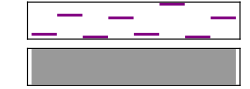

```mathematica
s1= Sound[{SoundNote[0],SoundNote[7],SoundNote[-1],SoundNote[6],SoundNote[0],SoundNote[11],SoundNote[-1],SoundNote[6]},{0,31}]
```

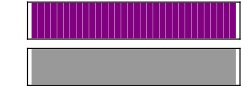

```mathematica
s2= Sound[Table[SoundNote[0,SoundVolume->1/6],{32}],{0,31}]
```

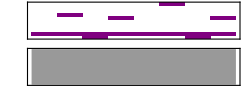

```mathematica
Sound[{s1,s2,Sound[SoundNote[0],{15.5,20}]}]
```

```mathematica
A:=Sound[SoundNote[0],{0,1}]
```

```mathematica
B:=Sound[SoundNote[1],{2,3}]
```

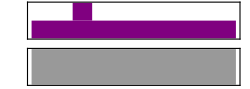

```mathematica
Sound[{A,B}]
```

```mathematica
Clear[A,B]
```

```mathematica
A[n_]:=Sound[SoundNote[n],{0,10}]
```

```mathematica
Sound[A[n],{n,0,10}]
```

Sound[Sound[SoundNote[n],{0,10}],{n,0,10}]

```mathematica
Sound[{Play[SoundNote[t],{t,0,20}]}]
```

Sound::ssnm: A good PlayRange could not be found since most of the samples are not evaluating to machine-sized real numbers.

Sound[{Sound[SampledSoundFunction[Function[{Play`Time5},Block[{t=0.+0.000125 Play`Time5},(SoundNote[t]+0.) 1.]],160000,8000]]}]

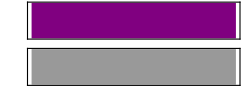

```mathematica
Sound[SoundNote["F"]]
```

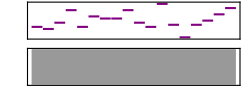

```mathematica
f1=Sound[{SoundNote[0],SoundNote[-1],SoundNote[2],SoundNote[8],SoundNote[0],SoundNote[5],SoundNote[4],Beep[];SoundNote[4],SoundNote[8],SoundNote[2],SoundNote[0],SoundNote[11],SoundNote[1],SoundNote[-5],SoundNote[1],SoundNote[3],SoundNote[6],SoundNote[9]},{0,5}]
```

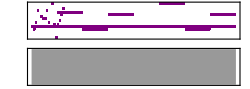

```mathematica
Sound[{f1,s1,s2},{0,20}]
```